## Import

```mathematica
datalist={};
SetDirectory[NotebookDirectory[]];
filenames=FileNames["*.csv"];
Do[
importfile=filenames[[j]];
data=Import[importfile,{"Data"}];
casedata=Cases[data,_?(AllTrue[#,NumberQ]&)];
AppendTo[datalist,casedata],
{j,1,Length@filenames}];
Length@datalist
```

8

## Data separation

```mathematica
λ=datalist[[1,All,1]];
mdeg=datalist[[All,All,2]];
V=datalist[[All,All,3]];
abs=datalist[[All,All,4]];
mCurves=datalist[[All,All,{1,2}]];
VCurves=datalist[[All,All,{1,3}]];
absCurves=datalist[[All,All,{1,4}]];
```

## Plots

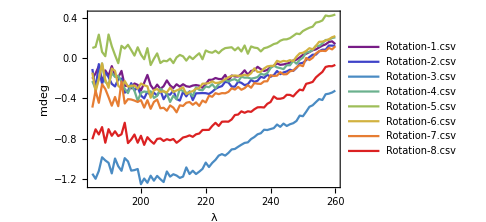
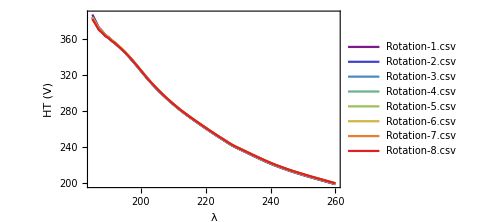
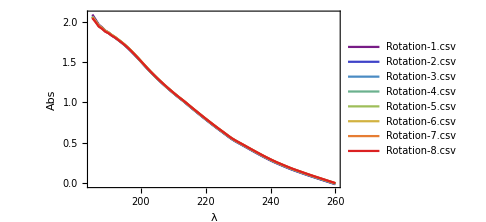

```mathematica
curvelist={mCurves,VCurves,absCurves};
ylabels={"mdeg","HT (V)","Abs"};
flabellist=Table[{"λ",ylabels[[i]]},{i,Length@ylabels}];
plotstyle={Frame->True,PlotStyle->"Rainbow"};
rawPlots=Table[
ListLinePlot[curvelist[[i]],
PlotLegends->filenames,
plotstyle,
FrameLabel->flabellist[[i]],ImageSize->Medium]
,{i,Length@curvelist}];
rawPlots//TableForm
```

## Average

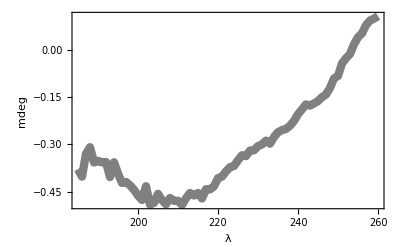

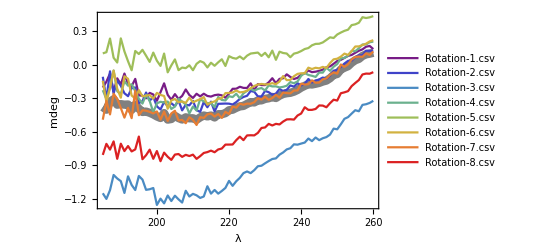

```mathematica
mdegAvg=Mean[mdeg];
mdegAvgCurve=Thread[{λ,mdegAvg}];
avgPlot=ListLinePlot[mdegAvgCurve,Frame->True,FrameLabel->flabellist[[1]],PlotStyle->{Thickness[0.015],Gray}]
Show[avgPlot,rawPlots[[1]],PlotRange->All]
```

## Baseline Subtracted & Averaged

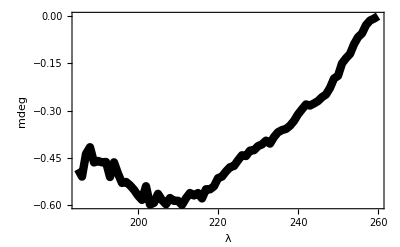

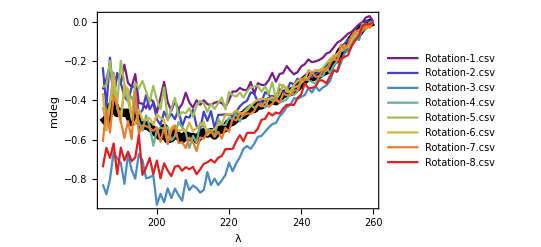

```mathematica
bsmdeg=Table[mdeg[[i]]-First@mdeg[[i]],{i,Length@mdeg}];
bsAvg=Mean[bsmdeg];
bscurvelist=Table[Thread[{λ,bsmdeg[[i]]}],{i,Length@bsmdeg}];
bsrawPlot=
ListLinePlot[bscurvelist,
PlotLegends->filenames,
plotstyle,
FrameLabel->flabellist[[1]],ImageSize->Medium];
bsAvgCurve=Thread[{λ,bsAvg}];
bsavgPlot=ListLinePlot[bsAvgCurve,Frame->True,FrameLabel->flabellist[[1]],PlotStyle->{Thickness[0.015],Black}]
Show[bsavgPlot,bsrawPlot,PlotRange->All]
```

## Comparison of Averages w/ & w/o Baseline Subtraction

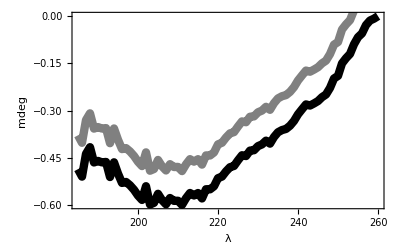

```mathematica
Show[bsavgPlot,avgPlot]
```

## 95% Confidence Intervals

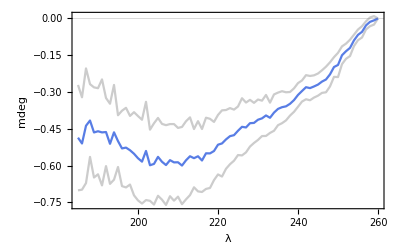

```mathematica
μ=Mean[bsmdeg];
μplot=Thread[{λ,μ}];
σ=StandardDeviation[bsmdeg];
CI95=σ  *1.96;
upperCI=MapThread[{#1[[1]],#1[[2]]+#2}&,{μplot,σ}];
lowerCI=MapThread[{#1[[1]],#1[[2]]-#2}&,{μplot,σ}];
perr=ListPlot[{lowerCI,upperCI},PlotStyle->GrayLevel[0.8],Joined->True,PlotTheme->{"Scientific","SansLabels"},FrameLabel->flabellist[[1]]];
pTheory=ListPlot[μplot,Joined->True,PlotStyle->ColorData[106][1],PlotTheme->{"Scientific","SansLabels"},FrameLabel->flabellist[[1]]];
Show[perr,pTheory]
```

## Data for export

### Average

```mathematica
bsAvgCurve//TableForm
```

260. | 0.
259. | -0.00797795
258. | -0.0139865
257. | -0.0284166
256. | -0.0548219
255. | -0.066947
254. | -0.0893759
253. | -0.120155
252. | -0.133724
251. | -0.15009
250. | -0.189683
249. | -0.198004
248. | -0.227985
247. | -0.248817
246. | -0.257419
245. | -0.269645
244. | -0.277248
243. | -0.283969
242. | -0.280341
241. | -0.295813
240. | -0.31182
239. | -0.332829
238. | -0.347939
237. | -0.358232
236. | -0.361777
235. | -0.368678
234. | -0.383803
233. | -0.404904
232. | -0.395375
231. | -0.407278
230. | -0.412794
229. | -0.425784
228. | -0.426928
227. | -0.444291
226. | -0.441736
225. | -0.457844
224. | -0.475722
223. | -0.479746
222. | -0.49302
221. | -0.509426
220. | -0.514555
219. | -0.540271
218. | -0.549981
217. | -0.549674
216. | -0.578915
215. | -0.561694
214. | -0.5695
213. | -0.561616
212. | -0.57816
211. | -0.599505
210. | -0.586207
209. | -0.586568
208. | -0.577536
207. | -0.597484
206. | -0.58418
205. | -0.564124
204. | -0.592803
203. | -0.598298
202. | -0.540046
201. | -0.583575
200. | -0.569745
199. | -0.551413
198. | -0.537114
197. | -0.52645
196. | -0.529729
195. | -0.499945
194. | -0.464144
193. | -0.510908
192. | -0.462977
191. | -0.46442
190. | -0.45975
189. | -0.46462
188. | -0.416082
187. | -0.437356
186. | -0.509617
185. | -0.485899

### Baseline subtracted (all)

```mathematica
bscurvelist
```

{{{260.,0.},{259.,0.027851},{258.,0.021215},{257.,-0.002444},{256.,-0.014695},{255.,-0.033161},{254.,-0.052409},{253.,-0.0609228},{252.,-0.0790569},{251.,-0.0962535},{250.,-0.107049},{249.,-0.131764},{248.,-0.154972},{247.,-0.162487},{246.,-0.184017},{245.,-0.195131},{244.,-0.202164},{243.,-0.206302},{242.,-0.192141},{241.,-0.216361},{240.,-0.228145},{239.,-0.257355},{238.,-0.267675},{237.,-0.249513},{236.,-0.225974},{235.,-0.261282},{234.,-0.266604},{233.,-0.305015},{232.,-0.260572},{231.,-0.297709},{230.,-0.322145},{229.,-0.322081},{228.,-0.312772},{227.,-0.367299},{226.,-0.306736},{225.,-0.348218},{224.,-0.347269},{223.,-0.337187},{222.,-0.354894},{221.,-0.355469},{220.,-0.399016},{219.,-0.435024},{218.,-0.413966},{217.,-0.407632},{216.,-0.412459},{215.,-0.424987},{214.,-0.419559},{213.,-0.399536},{212.,-0.42312},{211.,-0.399919},{210.,-0.437157},{209.,-0.41122},{208.,-0.361289},{207.,-0.419014},{206.,-0.446298},{205.,-0.403207},{204.,-0.453257},{203.,-0.409616},{202.,-0.306637},{201.,-0.386025},{200.,-0.462683},{199.,-0.406133},{198.,-0.392003},{197.,-0.440573},{196.,-0.416984},{195.,-0.414257},{194.,-0.266754},{193.,-0.331617},{192.,-0.311625},{191.,-0.218908},{190.,-0.315465},{189.,-0.261684},{188.,-0.381497},{187.,-0.219155},{186.,-0.291864},{185.,-0.344242}},{{260.,0.},{259.,0.000312},{258.,0.001193},{257.,-0.0401109},{256.,-0.0398306},{255.,-0.0556297},{254.,-0.0891274},{253.,-0.0899456},{252.,-0.113655},{251.,-0.143914},{250.,-0.170735},{249.,-0.177717},{248.,-0.22179},{247.,-0.251375},{246.,-0.239158},{245.,-0.256702},{244.,-0.266305},{243.,-0.283577},{242.,-0.25205},{241.,-0.294205},{240.,-0.309723},{239.,-0.289933},{238.,-0.32065},{237.,-0.309779},{236.,-0.349036},{235.,-0.360586},{234.,-0.341685},{233.,-0.382876},{232.,-0.392958},{231.,-0.370352},{230.,-0.358877},{229.,-0.407958},{228.,-0.407781},{227.,-0.366437},{226.,-0.359822},{225.,-0.402486},{224.,-0.413172},{223.,-0.430412},{222.,-0.459106},{221.,-0.480613},{220.,-0.472966},{219.,-0.471892},{218.,-0.473254},{217.,-0.474533},{216.,-0.541984},{215.,-0.454802},{214.,-0.505014},{213.,-0.457691},{212.,-0.546845},{211.,-0.530958},{210.,-0.447976},{209.,-0.488088},{208.,-0.482562},{207.,-0.532928},{206.,-0.445008},{205.,-0.495882},{204.,-0.468812},{203.,-0.495916},{202.,-0.457995},{201.,-0.525022},{200.,-0.496954},{199.,-0.412718},{198.,-0.446437},{197.,-0.373264},{196.,-0.450784},{195.,-0.46774},{194.,-0.327797},{193.,-0.334115},{192.,-0.405758},{191.,-0.380011},{190.,-0.312801},{189.,-0.26557},{188.,-0.381528},{187.,-0.183543},{186.,-0.432745},{185.,-0.232228}},{{260.,0.},{259.,-0.019001},{258.,-0.03067},{257.,-0.036495},{256.,-0.093562},{255.,-0.084305},{254.,-0.114485},{253.,-0.14617},{252.,-0.161168},{251.,-0.210276},{250.,-0.25506},{249.,-0.249071},{248.,-0.302446},{247.,-0.324627},{246.,-0.335058},{245.,-0.352115},{244.,-0.328592},{243.,-0.360903},{242.,-0.337771},{241.,-0.373746},{240.,-0.382795},{239.,-0.392623},{238.,-0.389765},{237.,-0.424465},{236.,-0.435054},{235.,-0.462277},{234.,-0.482292},{233.,-0.515406},{232.,-0.520848},{231.,-0.539138},{230.,-0.559395},{229.,-0.581017},{228.,-0.585777},{227.,-0.620679},{226.,-0.647161},{225.,-0.632306},{224.,-0.647254},{223.,-0.689529},{222.,-0.720099},{221.,-0.760949},{220.,-0.716839},{219.,-0.779759},{218.,-0.806979},{217.,-0.830829},{216.,-0.798039},{215.,-0.830659},{214.,-0.764819},{213.,-0.856439},{212.,-0.869309},{211.,-0.845839},{210.,-0.832929},{209.,-0.856569},{208.,-0.805309},{207.,-0.910649},{206.,-0.882029},{205.,-0.849309},{204.,-0.897019},{203.,-0.847419},{202.,-0.917979},{201.,-0.875739},{200.,-0.932029},{199.,-0.780609},{198.,-0.791659},{197.,-0.796869},{196.,-0.705049},{195.,-0.672607},{194.,-0.798529},{193.,-0.753209},{192.,-0.675957},{191.,-0.824759},{190.,-0.719049},{189.,-0.695289},{188.,-0.6639},{187.,-0.799919},{186.,-0.878089},{185.,-0.827449}},{{260.,0.},{259.,-0.005757},{258.,-0.025414},{257.,-0.025699},{256.,-0.059774},{255.,-0.086216},{254.,-0.083657},{253.,-0.125893},{252.,-0.145599},{251.,-0.150508},{250.,-0.201391},{249.,-0.224697},{248.,-0.261814},{247.,-0.233062},{246.,-0.277794},{245.,-0.277343},{244.,-0.315998},{243.,-0.30607},{242.,-0.298449},{241.,-0.281224},{240.,-0.306279},{239.,-0.356583},{238.,-0.372504},{237.,-0.362089},{236.,-0.39541},{235.,-0.404835},{234.,-0.41043},{233.,-0.40071},{232.,-0.401102},{231.,-0.39197},{230.,-0.4373},{229.,-0.415651},{228.,-0.423709},{227.,-0.439264},{226.,-0.422422},{225.,-0.440982},{224.,-0.463229},{223.,-0.507907},{222.,-0.466765},{221.,-0.496293},{220.,-0.48891},{219.,-0.526449},{218.,-0.522334},{217.,-0.496006},{216.,-0.586315},{215.,-0.550451},{214.,-0.551406},{213.,-0.535447},{212.,-0.515397},{211.,-0.616749},{210.,-0.581087},{209.,-0.643365},{208.,-0.561834},{207.,-0.537343},{206.,-0.509998},{205.,-0.581549},{204.,-0.603227},{203.,-0.536616},{202.,-0.545528},{201.,-0.538624},{200.,-0.552372},{199.,-0.630882},{198.,-0.531227},{197.,-0.476486},{196.,-0.554886},{195.,-0.511792},{194.,-0.443578},{193.,-0.38191},{192.,-0.394324},{191.,-0.354442},{190.,-0.469627},{189.,-0.444321},{188.,-0.259215},{187.,-0.410439},{186.,-0.513948},{185.,-0.434909}},{{260.,0.},{259.,-0.010777},{258.,-0.016849},{257.,-0.00979},{256.,-0.059325},{255.,-0.07362},{254.,-0.080458},{253.,-0.121372},{252.,-0.131737},{251.,-0.146983},{250.,-0.164572},{249.,-0.195496},{248.,-0.189792},{247.,-0.213136},{246.,-0.23554},{245.,-0.247181},{244.,-0.248623},{243.,-0.261123},{242.,-0.285714},{241.,-0.294322},{240.,-0.312641},{239.,-0.327594},{238.,-0.335752},{237.,-0.367753},{236.,-0.334781},{235.,-0.330054},{234.,-0.318162},{233.,-0.391086},{232.,-0.308543},{231.,-0.368577},{230.,-0.328346},{229.,-0.356619},{228.,-0.326203},{227.,-0.330509},{226.,-0.334869},{225.,-0.353894},{224.,-0.38583},{223.,-0.361007},{222.,-0.380975},{221.,-0.373972},{220.,-0.358245},{219.,-0.446046},{218.,-0.386059},{217.,-0.413334},{216.,-0.444346},{215.,-0.417171},{214.,-0.459224},{213.,-0.416624},{212.,-0.402595},{211.,-0.427143},{210.,-0.484182},{209.,-0.440002},{208.,-0.465726},{207.,-0.460509},{206.,-0.483287},{205.,-0.387298},{204.,-0.441097},{203.,-0.503116},{202.,-0.334843},{201.,-0.445457},{200.,-0.399114},{199.,-0.326477},{198.,-0.409552},{197.,-0.354213},{196.,-0.301773},{195.,-0.339159},{194.,-0.311983},{193.,-0.484773},{192.,-0.40395},{191.,-0.315706},{190.,-0.199308},{189.,-0.415287},{188.,-0.372397},{187.,-0.200386},{186.,-0.322692},{185.,-0.333402}},{{260.,0.},{259.,-0.01096},{258.,-0.031461},{257.,-0.043896},{256.,-0.05537},{255.,-0.056421},{254.,-0.097577},{253.,-0.131609},{252.,-0.120038},{251.,-0.147253},{250.,-0.165714},{249.,-0.171347},{248.,-0.204739},{247.,-0.249111},{246.,-0.238883},{245.,-0.251976},{244.,-0.246658},{243.,-0.257824},{242.,-0.245888},{241.,-0.296003},{240.,-0.296031},{239.,-0.301577},{238.,-0.322474},{237.,-0.355371},{236.,-0.357491},{235.,-0.321004},{234.,-0.369662},{233.,-0.393632},{232.,-0.384351},{231.,-0.393921},{230.,-0.395893},{229.,-0.39166},{228.,-0.396605},{227.,-0.409645},{226.,-0.429368},{225.,-0.451468},{224.,-0.463236},{223.,-0.466923},{222.,-0.450368},{221.,-0.467893},{220.,-0.472323},{219.,-0.473593},{218.,-0.518943},{217.,-0.523414},{216.,-0.548232},{215.,-0.557445},{214.,-0.577503},{213.,-0.508956},{212.,-0.527802},{211.,-0.541172},{210.,-0.556182},{209.,-0.513151},{208.,-0.56109},{207.,-0.548412},{206.,-0.555978},{205.,-0.52667},{204.,-0.538707},{203.,-0.61332},{202.,-0.499324},{201.,-0.489592},{200.,-0.471692},{199.,-0.52388},{198.,-0.491232},{197.,-0.496222},{196.,-0.502089},{195.,-0.446905},{194.,-0.522272},{193.,-0.494879},{192.,-0.345359},{191.,-0.322724},{190.,-0.51468},{189.,-0.433363},{188.,-0.271955},{187.,-0.428257},{186.,-0.55364},{185.,-0.363193}},{{260.,0.},{259.,-0.0316443},{258.,-0.017115},{257.,-0.0482191},{256.,-0.045626},{255.,-0.0494946},{254.,-0.0722731},{253.,-0.115622},{252.,-0.137936},{251.,-0.116935},{250.,-0.1989},{249.,-0.187403},{248.,-0.210479},{247.,-0.242556},{246.,-0.249616},{245.,-0.278658},{244.,-0.280215},{243.,-0.258592},{242.,-0.293138},{241.,-0.296373},{240.,-0.288809},{239.,-0.348951},{238.,-0.35021},{237.,-0.375242},{236.,-0.373446},{235.,-0.367185},{234.,-0.413642},{233.,-0.387856},{232.,-0.417432},{231.,-0.433623},{230.,-0.405614},{229.,-0.431713},{228.,-0.419093},{227.,-0.4546},{226.,-0.468808},{225.,-0.467095},{224.,-0.477277},{223.,-0.467582},{222.,-0.503389},{221.,-0.492901},{220.,-0.560002},{219.,-0.54095},{218.,-0.594705},{217.,-0.559942},{216.,-0.583245},{215.,-0.555813},{214.,-0.563129},{213.,-0.595017},{212.,-0.588635},{211.,-0.658279},{210.,-0.611859},{209.,-0.589545},{208.,-0.642585},{207.,-0.612991},{206.,-0.618003},{205.,-0.531435},{204.,-0.555041},{203.,-0.623086},{202.,-0.537721},{201.,-0.611216},{200.,-0.537038},{199.,-0.555188},{198.,-0.541153},{197.,-0.530676},{196.,-0.527099},{195.,-0.570847},{194.,-0.350943},{193.,-0.597341},{192.,-0.505448},{191.,-0.592578},{190.,-0.506737},{189.,-0.425885},{188.,-0.3785},{187.,-0.563956},{186.,-0.44224},{185.,-0.611118}},{{260.,0.},{259.,-0.0138473},{258.,-0.0127912},{257.,-0.0206789},{256.,-0.0703926},{255.,-0.0967286},{254.,-0.125021},{253.,-0.169706},{252.,-0.180606},{251.,-0.1886},{250.,-0.25404},{249.,-0.246538},{248.,-0.27785},{247.,-0.314185},{246.,-0.299288},{245.,-0.298052},{244.,-0.329428},{243.,-0.337361},{242.,-0.337576},{241.,-0.314271},{240.,-0.370136},{239.,-0.388016},{238.,-0.424483},{237.,-0.421648},{236.,-0.423027},{235.,-0.442199},{234.,-0.467944},{233.,-0.462655},{232.,-0.477192},{231.,-0.462931},{230.,-0.494781},{229.,-0.499577},{228.,-0.543482},{227.,-0.565892},{226.,-0.5647},{225.,-0.566302},{224.,-0.608506},{223.,-0.577418},{222.,-0.608564},{221.,-0.647321},{220.,-0.648138},{219.,-0.648451},{218.,-0.683608},{217.,-0.691701},{216.,-0.716702},{215.,-0.702224},{214.,-0.71535},{213.,-0.723215},{212.,-0.751576},{211.,-0.775983},{210.,-0.738286},{209.,-0.750603},{208.,-0.739897},{207.,-0.758024},{206.,-0.732837},{205.,-0.737646},{204.,-0.785264},{203.,-0.757298},{202.,-0.720345},{201.,-0.796928},{200.,-0.706079},{199.,-0.77542},{198.,-0.693651},{197.,-0.743301},{196.,-0.779172},{195.,-0.576256},{194.,-0.691297},{193.,-0.709421},{192.,-0.661399},{191.,-0.706236},{190.,-0.640335},{189.,-0.775564},{188.,-0.619664},{187.,-0.693192},{186.,-0.641718},{185.,-0.74065}}}